```mathematica
m = 1
h = 1
w = 1
Xi[x_] = Sqrt[m*w/h]*x
Xif[x_] = Sqrt[mf*wf/hf]*x
HPsi[x_,n_] = HermiteH[n,Xi[x]]*(m*w/(Pi*h))^(1/4)*1/Sqrt[(2^n*n!)]*Exp[-Xi[x]^2/2]
HPsif[x_,n_] = HermiteH[n,Xif[x]]*(mf*wf/(Pi*hf))^(1/4)*1/Sqrt[(2^n*n!)]*Exp[-Xif[x]^2/2]
```

1

1

1

x

√((mf wf)/hf) x

(ⅇ^(-x^2/2) HermiteH[n,x])/(π^(1/4) √(2^n n!))

(ⅇ^(-(mf wf x^2)/(2 hf)) ((mf wf)/hf)^(1/4) HermiteH[n,√((mf wf)/hf) x])/(π^(1/4) √(2^n n!))

```mathematica
Manipulate[Plot[HPsi[x,n],{x,-5,5}],{n,0,10}]
```

```mathematica
Integrate[(HPsif[x,0])(HPsif[x,0]),{x,-Infinity,Infinity}]
Integrate[(HPsif[x,1])(HPsif[x,1]),{x,-Infinity,Infinity}]
Integrate[(HPsif[x,0])(HPsif[x,1]),{x,-Infinity,Infinity}]
Integrate[(HPsif[x,0])x(HPsif[x,1]),{x,-Infinity,Infinity}]
Integrate[(HPsif[x,1])x^2(HPsif[x,1]),{x,-Infinity,Infinity}]
1/2*Integrate[(HPsif[x,0]+HPsif[x,2])*x*(HPsif[x,0]+HPsif[x,2]),{x,-Infinity,Infinity}]
```

ConditionalExpression[1, Re[(mf wf)/hf]>0]

ConditionalExpression[1, Re[(mf wf)/hf]>0]

ConditionalExpression[0, Re[(mf wf)/hf]≥0]

ConditionalExpression[(mf wf)/(√2 hf ((mf wf)/hf)^(3/2)), Re[(mf wf)/hf]>0]

ConditionalExpression[(3 hf)/(2 mf wf), Re[(mf wf)/hf]>0]

Integrate::idiv: Integral of (ⅇ^(-(mf wf x^2)/hf) √((mf wf)/hf) x ((-2+√2) hf-2 √2 mf wf x^2)^2)/(4 hf^2 √π) does not converge on {-∞,∞}.

1/2 ∫_(-∞)^∞ x ((ⅇ^(-(mf wf x^2)/(2 hf)) ((mf wf)/hf)^(1/4))/π^(1/4)+(ⅇ^(-(mf wf x^2)/(2 hf)) ((mf wf)/hf)^(1/4) (-2+(4 mf wf x^2)/hf))/(2 √2 π^(1/4)))^2ⅆx

ConditionalExpression[(mf wf)/(√2 hf ((mf wf)/hf)^(3/2)), Re[(mf wf)/hf]>0]

I

-2+4 x^2

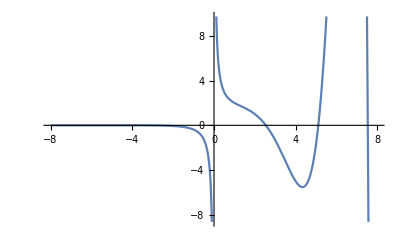

HermiteH[x,1]

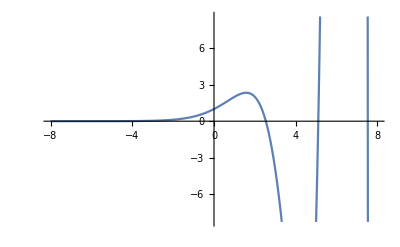

x ((ⅇ^(-x^2/2))/π^(1/4)+(√2 ⅇ^(-x^2/2) x)/π^(1/4))^2

√2

(ⅇ^(-x^2) (-3-2 √2 x-2 x^2+ⅇ^(x^2) √(2 π) Erf[x]))/(2 √π)

```mathematica
ConditionalExpression[(mf wf)/(√2 hf ((mf wf)/hf)^(3/2)), Re[(mf wf)/hf]>0]
```